Evaluate the evaluation cells of the other important notebooks

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"directMat-2.nb",EvaluationElements->Automatic];
NotebookEvaluate[NotebookDirectory[]<>"periods.nb",EvaluationElements->Automatic];
NotebookEvaluate[NotebookDirectory[]<>"WeylTest.nb",EvaluationElements->Automatic];
```

Given some function f_L[k,l] generate the corresponding matrix

```mathematica
DirectFMat[L_,f_]:=Module[{k,n,l,tempMat},
tempMat=ConstantArray[0,{L,L}];
Do[tempMat[[k,l]]=f[L,k,l];
,{k,1,L},{l,1,L}];
Return[tempMat,Module];
]
```

```mathematica
DirectFMatN[L_,f_,NPrec_]:=
Module[{k,n,l,tempMat},
tempMat=ConstantArray[0,{L,L}];
Do[tempMat[[k,l]]=N[f[L,k,l],NPrec];
,{k,1,L},{l,1,L}];
Return[tempMat,Module];
]
```

C matrix  for X_m X_n , which computes ∂^m X ∂^n X one point function on the disk when m,n are positive integer.

```mathematica
DirectCMat[L_,m_,n_]:=DirectFMat[L,(((Abs[m]!)(Abs[n]!))/#1^2 Exp[-I*2*Pi*(m*#2+n*#3)/#1])&]
DirectCMatN[L_,m_,n_,NPrec_]:=DirectFMatN[L,(((Abs[m]!)(Abs[n]!))/#1^2 Exp[-I*2*Pi*(m*#2+n*#3)/#1])&,NPrec]
```

```mathematica
DirectTracedCMat[L_,m_,n_,l1_,l2_]:=
DirectTracedMat[L,l1,l2,DirectCMat[L,m,n]]
```

```mathematica
DirectTracedCMatN[L_,m_,n_,l1_,l2_,NPrec_]:=
DirectTracedMat[L,l1,l2,DirectCMatN[L,m,n,NPrec]]
```

### Generate Analytic Formula For ∂^n X ∂X

Compute the disk one point function by the conformal transformation of one point function on the torus

```mathematica
Ord=4;
u[z_]:=Integrate[fHatS[a],{a,0,z}]
uTrun[z_]:=Series[u[z],{z,0,Ord+3}]
T2=Simplify[Series[fHatS[z]fHatS[0] (-1/(2 π)1/uTrun[z]^2+Sum[1/(n!)uTrun[z]^n CorrelatorT2[n],{n,0,Ord}]),{z,0,Ord}],Assumptions->Table[Derivative[2k-1][fHatS][0]==0,{k,1,Ord+3}]];
D2=-1/(2 π)1/z^2+Sum[1/(n!)z^n CorrelatorD2[n],{n,0,Ord}];
CorT2=CoefficientList[Series[1/(2Pi)D[Log[1/2(EllipticTheta[1,Pi U,ⅇ^(π I τ)]-EllipticTheta[1,-Pi U,ⅇ^(π I τ)])],{U,2}]+1/(2 Im[τ])+1/(2Pi U^2),{U,0,Ord}]//Normal,{U}];
replist=Table[CorrelatorT2[n-1]->(n-1)!CorT2[[n]],{n,1,Length[CorT2]}];
T2List=ReplaceAll[CoefficientList[T2+1/(2 π z^2),z],replist];
MatchingList=Simplify[MapIndexed[#1*Factorial[First[#2]-1]&,T2List]]
```

{-fHatS''[0]/(12 π fHatS[0])+1/6 fHatS[0]^2 (3/Im[τ]+(π EllipticThetaPrime^(0,2,0)[1,0,ⅇ^(ⅈ π τ)])/EllipticThetaPrime[1,0,ⅇ^(ⅈ π τ)]),0,1/(120 π fHatS[0]^2)(10 fHatS''[0]^2-3 fHatS[0] fHatS^(4)[0]+20 π fHatS[0]^3 fHatS''[0] (3/Im[τ]+(π EllipticThetaPrime^(0,2,0)[1,0,ⅇ^(ⅈ π τ)])/EllipticThetaPrime[1,0,ⅇ^(ⅈ π τ)])+(4 π^4 fHatS[0]^6 (-5 (EllipticThetaPrime^(0,2,0)[1,0,ⅇ^(ⅈ π τ)])^2+3 EllipticThetaPrime[1,0,ⅇ^(ⅈ π τ)] EllipticThetaPrime^(0,4,0)[1,0,ⅇ^(ⅈ π τ)]))/EllipticThetaPrime[1,0,ⅇ^(ⅈ π τ)]^2),0,1/(252 π fHatS[0]^3)(-70 fHatS''[0]^3+(126 π fHatS[0]^4 fHatS^(4)[0])/Im[τ]+42 fHatS[0] fHatS''[0] fHatS^(4)[0]-3 fHatS[0]^2 fHatS^(6)[0]+(140 π^6 fHatS[0]^9 (EllipticThetaPrime^(0,2,0)[1,0,ⅇ^(ⅈ π τ)])^3)/(EllipticThetaPrime[1,0,ⅇ^(ⅈ π τ)]^3)-(42 π^4 fHatS[0]^6 EllipticThetaPrime^(0,2,0)[1,0,ⅇ^(ⅈ π τ)] (10 fHatS''[0] EllipticThetaPrime^(0,2,0)[1,0,ⅇ^(ⅈ π τ)]+3 π^2 fHatS[0]^3 EllipticThetaPrime^(0,4,0)[1,0,ⅇ^(ⅈ π τ)]))/EllipticThetaPrime[1,0,ⅇ^(ⅈ π τ)]^2+(6 (7 π^2 fHatS[0]^4 fHatS^(4)[0] EllipticThetaPrime^(0,2,0)[1,0,ⅇ^(ⅈ π τ)]+42 π^4 fHatS[0]^6 fHatS''[0] EllipticThetaPrime^(0,4,0)[1,0,ⅇ^(ⅈ π τ)]+3 π^6 fHatS[0]^9 EllipticThetaPrime^(0,6,0)[1,0,ⅇ^(ⅈ π τ)]))/EllipticThetaPrime[1,0,ⅇ^(ⅈ π τ)])}

### Calculating tr(CA^-1):

```mathematica
setL=310;
prec=15;
AMat=DirectMatN[setL,prec];
```

FindTrCA has the input (L,l1,l2) as usual.  s is an integer indicating that it is computing :∂^s X ∂X:  on the disk.  
One has to input the correct CMat for :∂^s X ∂X:  to get the correct matching.
The output is {τ, Analytic result for one point function, numerical result for one-point function}

```mathematica
findTrCA[L_,l1_,l2_,s_,AMat_,CMat_]:=Module[{l3,redA,invA,redC,tr,f,DerList,fHat,f0,df,ddf,per,perRed,AnalyticTest,NumericalTest,Formula,ReplaceTable},
l3=L/2-l1-l2;
(*Print[1];*)
redA=DirectRedTracedMat[L,l1,l2,AMat];
(*Print[1];*)
redC=DirectRedTracedMat[L,l1,l2,CMat];
(*Print[2];*)
invA=Inverse[redA];
(*Print[3]*)
f=CylEqnFastOptimized[l1,l2,l3,z];
(*Print[4];*)
NumericalTest=Tr[redC . invA];
per=PeriodsFastGivenF[l1,l2,l3,l1/2,l2/2,l3/2,f,z]//N;
perRed=per/per[[1]];
fHat=f/per[[1]];
(*Print[1/(1-perRed[[2]])];*)
DerList=Table[D[fHat,{z,n}]/.{z->0},{n,0,s+1}];
ReplaceTable=Join[{fHatS[0]->DerList[[1]]},Table[{Derivative[n][fHatS][0]->DerList[[n+1]]},{n,1,s+1}]]//Flatten;
AnalyticTest=MatchingList[[s]]/.ReplaceTable/.{τ->perRed[[2]],z->0}//N;
(*Note that 1/per[[1]] is \hat{f}(0)*)
Return[{perRed[[2]],AnalyticTest,NumericalTest},Module]
]
```

Test Timing

```mathematica
findTrCA[setL,3,3,1,AMat,CMat11]//Timing
```

{1.8151,{0.934524+0.355899 ⅈ,0.0830165-0.0118579 ⅈ,0.08471492326232-0.01210051741401 ⅈ}}

Compute  :∂X∂X: one point function

```mathematica
(*Since we want to test different τ at the same L, useful to store the precursor matrices*)
CMat11=DirectCMatN[setL,1,1,prec];
L1=Table[
Print[k];
findTrCA[setL,k,k,1,AMat,CMat11]
,{k,1,77,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

33

35

37

39

41

43

45

47

49

51

53

55

57

59

61

63

65

67

69

71

73

75

77

{{0.96148+0.274875 ⅈ,0.119554-0.00727848 ⅈ,0.1016753193191-0.00619000027459 ⅈ},{0.934524+0.355899 ⅈ,0.0830165-0.0118579 ⅈ,0.08471492326232-0.01210051741401 ⅈ},{0.916834+0.399269 ⅈ,0.0733468-0.0166293 ⅈ,0.07358956997391-0.01668428749026 ⅈ},{0.900453+0.434952 ⅈ,0.0639274-0.0200574 ⅈ,0.06431884035513-0.0201801663495 ⅈ},{0.885045+0.465505 ⅈ,0.0558512-0.0226385 ⅈ,0.05607961804688-0.02273112448912 ⅈ},{0.869982+0.493084 ⅈ,0.0483625-0.024334 ⅈ,0.04858275718273-0.02444486362547 ⅈ},{0.855128+0.518417 ⅈ,0.0415459-0.0253148 ⅈ,0.04171008909347-0.0254148428899 ⅈ},{0.840281+0.542151 ⅈ,0.0352662-0.0256224 ⅈ,0.03541210826229-0.02572840265888 ⅈ},{0.825372+0.56459 ⅈ,0.0295533-0.0253707 ⅈ,0.02966906662325-0.025470058255 ⅈ},{0.810299+0.586017 ⅈ,0.0243746-0.0246229 ⅈ,0.02447337546572-0.02472265807915 ⅈ},{0.795015+0.60659 ⅈ,0.0197419-0.0234737 ⅈ,0.01982073963129-0.02356749302204 ⅈ},{0.779455+0.626458 ⅈ,0.0156407-0.0219928 ⅈ,0.0157054155943-0.02208386393595 ⅈ},{0.76358+0.645713 ⅈ,0.0120673-0.0202638 ⅈ,0.01211764584529-0.02034837243014 ⅈ},{0.747341+0.664441 ⅈ,0.00900324-0.0183544 ⅈ,0.009042351699305-0.01843408768104 ⅈ},{0.730699+0.6827 ⅈ,0.00642999-0.016337 ⅈ,0.006458610921512-0.01640968419365 ⅈ},{0.713611+0.700542 ⅈ,0.00431952-0.0142721 ⅈ,0.00433965505442-0.0143386130904 ⅈ},{0.696039+0.718004 ⅈ,0.00264045-0.0122192 ⅈ,0.0026532260251-0.01227834976292 ⅈ},{0.677937+0.73512 ⅈ,0.00135527-0.0102275 ⅈ,0.00136218729829-0.01027974764896 ⅈ},{0.659265+0.75191 ⅈ,0.000423046-0.00834175 ⅈ,0.000425316085-0.008386518566678 ⅈ},{0.639976+0.768395 ⅈ,-0.000200631-0.00659714 ⅈ,-0.00020177835289-0.006634852954108 ⅈ},{0.620023+0.784584 ⅈ,-0.000562231-0.00502261 ⅈ,-0.000565653535359-0.00505318773814 ⅈ},{0.599352+0.800486 ⅈ,-0.000709328-0.00363824 ⅈ,-0.000713984934258-0.00366212498181 ⅈ},{0.577907+0.816102 ⅈ,-0.000689601-0.00245705 ⅈ,-0.000694498630028-0.00247450071711 ⅈ},{0.555628+0.831431 ⅈ,-0.000549628-0.00148404 ⅈ,-0.0005539095518-0.00149560036585 ⅈ},{0.532446+0.846464 ⅈ,-0.000334008-0.000717337 ⅈ,-0.00033688472753-0.000723514854649 ⅈ},{0.508285+0.861189 ⅈ,-0.0000842304-0.000148195 ⅈ,-0.000085046230634-0.00014962996943 ⅈ},{0.483062+0.875586 ⅈ,0.000162183+0.000238125 ⅈ,0.00016397674011+0.00024075924925 ⅈ},{0.456679+0.889632 ⅈ,0.000372612+0.000461729 ⅈ,0.00037744355286+0.00046771703765 ⅈ},{0.429026+0.903292 ⅈ,0.000520194+0.000547244 ⅈ,0.000528350905998+0.000555824837435 ⅈ},{0.399976+0.916526 ⅈ,0.000584595+0.000522807 ⅈ,0.000596252176025+0.000533231796996 ⅈ},{0.369374+0.929281 ⅈ,0.000552916+0.000419098 ⅈ,0.000568084415123+0.00043059491967 ⅈ},{0.337039+0.941491 ⅈ,0.000420497+0.000268053 ⅈ,0.00043907438576+0.00027989503086 ⅈ},{0.302741+0.953073 ⅈ,0.000192157+0.000101617 ⅈ,0.00021386099681+0.00011309486184 ⅈ},{0.266188+0.963921 ⅈ,-0.000116301-0.0000499088 ⅈ,-0.00009188901808-0.00003943268324 ⅈ},{0.226986+0.973898 ⅈ,-0.000475265-0.000159766 ⅈ,-0.00044876637811-0.00015085782601 ⅈ},{0.184568+0.98282 ⅈ,-0.000836059-0.000207453 ⅈ,-0.00080830792358-0.000200567321 ⅈ},{0.138028+0.990428 ⅈ,-0.00111855-0.000182976 ⅈ,-0.00109064953071-0.00017841156157 ⅈ},{0.0856363+0.996326 ⅈ,-0.00117426-0.0000954105 ⅈ,-0.00114736041362-0.000093224703939 ⅈ},{0.0222687+0.999752 ⅈ,-0.000594619-5.14657×10^-13 ⅈ,-0.00055418445831+0. ⅈ}}

x axis is Reτ, y axis is the real part of the 1 point function

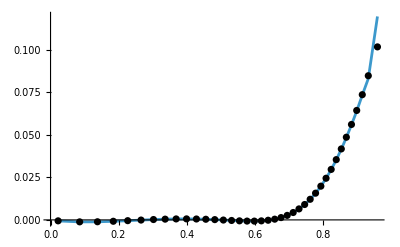

```mathematica
Show[ListLinePlot[Re[L1[[All,{1,2}]]]],ListPlot[Re[L1[[All,{1,3}]]],PlotStyle->{Black}]]
```

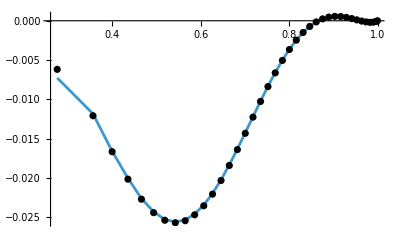

```mathematica
Show[ListLinePlot[Im[L1[[All,{1,2}]]]],ListPlot[Im[L1[[All,{1,3}]]],PlotStyle->{Black}]]
```

```mathematica
CMat21=DirectCMatN[setL,2,1,prec];
```

```mathematica
L12=Table[
Print[k];
findTrCA[setL,k,k,2,AMat,CMat21]
,{k,1,77,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

33

35

37

39

41

43

45

47

49

51

53

55

57

59

61

63

65

67

69

71

73

75

77

{{0.96148+0.274875 ⅈ,0.,0.+0. ⅈ},{0.934524+0.355899 ⅈ,0.,0.+0. ⅈ},{0.916834+0.399269 ⅈ,0.,0.+0. ⅈ},{0.900453+0.434952 ⅈ,0.,0.+0. ⅈ},{0.885045+0.465505 ⅈ,0.,0.+0. ⅈ},{0.869982+0.493084 ⅈ,0.,0.+0. ⅈ},{0.855128+0.518417 ⅈ,0.,0.+0. ⅈ},{0.840281+0.542151 ⅈ,0.,0.+0. ⅈ},{0.825372+0.56459 ⅈ,0.,0.+0. ⅈ},{0.810299+0.586017 ⅈ,0.,0.+0. ⅈ},{0.795015+0.60659 ⅈ,0.,0.+0. ⅈ},{0.779455+0.626458 ⅈ,0.,0.+0. ⅈ},{0.76358+0.645713 ⅈ,0.,0.+0. ⅈ},{0.747341+0.664441 ⅈ,0.,0.+0. ⅈ},{0.730699+0.6827 ⅈ,0.,0.+0. ⅈ},{0.713611+0.700542 ⅈ,0.,0.+0. ⅈ},{0.696039+0.718004 ⅈ,0.,0.+0. ⅈ},{0.677937+0.73512 ⅈ,0.,0.+0. ⅈ},{0.659265+0.75191 ⅈ,0.,0.+0. ⅈ},{0.639976+0.768395 ⅈ,0.,0.+0. ⅈ},{0.620023+0.784584 ⅈ,0.,0.+0. ⅈ},{0.599352+0.800486 ⅈ,0.,0.+0. ⅈ},{0.577907+0.816102 ⅈ,0.,0.+0. ⅈ},{0.555628+0.831431 ⅈ,0.,0.+0. ⅈ},{0.532446+0.846464 ⅈ,0.,0.+0. ⅈ},{0.508285+0.861189 ⅈ,0.,0.+0. ⅈ},{0.483062+0.875586 ⅈ,0.,0.+0. ⅈ},{0.456679+0.889632 ⅈ,0.,0.+0. ⅈ},{0.429026+0.903292 ⅈ,0.,0.+0. ⅈ},{0.399976+0.916526 ⅈ,0.,0.+0. ⅈ},{0.369374+0.929281 ⅈ,0.,0.+0. ⅈ},{0.337039+0.941491 ⅈ,0.,0.+0. ⅈ},{0.302741+0.953073 ⅈ,0.,0.+0. ⅈ},{0.266188+0.963921 ⅈ,0.,0.+0. ⅈ},{0.226986+0.973898 ⅈ,0.,0.+0. ⅈ},{0.184568+0.98282 ⅈ,0.,0.+0. ⅈ},{0.138028+0.990428 ⅈ,0.,0.+0. ⅈ},{0.0856363+0.996326 ⅈ,0.,0.+0. ⅈ},{0.0222687+0.999752 ⅈ,0.,0.+0. ⅈ}}

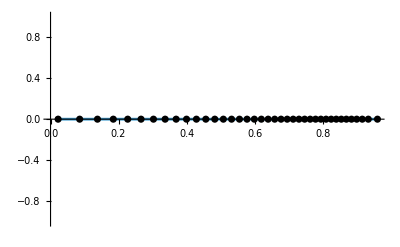

```mathematica
Show[ListLinePlot[Re[L12[[All,{1,2}]]]],ListPlot[Re[L12[[All,{1,3}]]],PlotStyle->{Black}]]
```

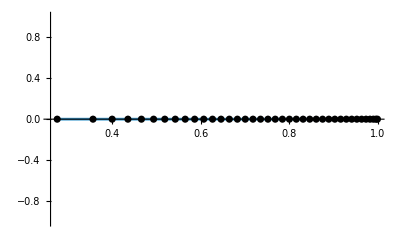

```mathematica
Show[ListLinePlot[Im[L12[[All,{1,2}]]]],ListPlot[Im[L12[[All,{1,3}]]],PlotStyle->{Black}]]
```

```mathematica
CMat31=DirectCMatN[setL,3,1,prec];
```

```mathematica
L13=Table[
Print[k];
findTrCA[setL,k,k,3,AMat,CMat31]
,{k,1,77,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

33

35

37

39

41

43

45

47

49

51

53

55

57

59

61

63

65

67

69

71

73

75

77

{{0.96148+0.274875 ⅈ,-0.157877+0.0192946 ⅈ,-0.11371076449+0.0138969453675 ⅈ},{0.934524+0.355899 ⅈ,-0.139928+0.0408068 ⅈ,-0.140611703012+0.0410060476363 ⅈ},{0.916834+0.399269 ⅈ,-0.150113+0.071756 ⅈ,-0.1489409163186+0.071195634148 ⅈ},{0.900453+0.434952 ⅈ,-0.146767+0.102153 ⅈ,-0.1464656325435+0.101943088928 ⅈ},{0.885045+0.465505 ⅈ,-0.135494+0.131436 ⅈ,-0.1351684324074+0.1311201992495 ⅈ},{0.869982+0.493084 ⅈ,-0.116546+0.15704 ⅈ,-0.1164260778266+0.1568785332725 ⅈ},{0.855128+0.518417 ⅈ,-0.0917453+0.177827 ⅈ,-0.09166739821505+0.1776759565682 ⅈ},{0.840281+0.542151 ⅈ,-0.0625062+0.192374 ⅈ,-0.06249309831194+0.1923339798617 ⅈ},{0.825372+0.56459 ⅈ,-0.0306522+0.200087 ⅈ,-0.030652499111+0.2000889462421 ⅈ},{0.810299+0.586017 ⅈ,0.00203237+0.200539 ⅈ,0.002033214633+0.2006227503454 ⅈ},{0.795015+0.60659 ⅈ,0.0337477+0.193946 ⅈ,0.0337688206776+0.1940671660972 ⅈ},{0.779455+0.626458 ⅈ,0.0628284+0.180812 ⅈ,0.06288696574718+0.1809803724934 ⅈ},{0.76358+0.645713 ⅈ,0.0878438+0.162114 ⅈ,0.08794288566448+0.1622973530998 ⅈ},{0.747341+0.664441 ⅈ,0.107645+0.139066 ⅈ,0.1077938106704+0.139258122777 ⅈ},{0.730699+0.6827 ⅈ,0.121467+0.113142 ⅈ,0.1216573722582+0.1133193463754 ⅈ},{0.713611+0.700542 ⅈ,0.128915+0.0859023 ⅈ,0.1291455865503+0.08605588383763 ⅈ},{0.696039+0.718004 ⅈ,0.130018+0.0589436 ⅈ,0.1302731360612+0.05905914406829 ⅈ},{0.677937+0.73512 ⅈ,0.12517+0.033766 ⅈ,0.12544064022+0.03383890585462 ⅈ},{0.659265+0.75191 ⅈ,0.115128+0.0117074 ⅈ,0.1153952954147+0.0117345546072 ⅈ},{0.639976+0.768395 ⅈ,0.10092-0.00614401 ⅈ,0.1011725903163-0.00615939409911 ⅈ},{0.620023+0.784584 ⅈ,0.0838012-0.0189995 ⅈ,0.08402370801567-0.0190499238007 ⅈ},{0.599352+0.800486 ⅈ,0.0651499-0.0264077 ⅈ,0.06533370051259-0.0264821432708 ⅈ},{0.577907+0.816102 ⅈ,0.0463982-0.0282714 ⅈ,0.04653559123935-0.0283551238044 ⅈ},{0.555628+0.831431 ⅈ,0.0289353-0.0248401 ⅈ,0.0290252892079-0.0249173934719 ⅈ},{0.532446+0.846464 ⅈ,0.0140362-0.0166895 ⅈ,0.0140816685659-0.0167435540671 ⅈ},{0.508285+0.861189 ⅈ,0.00278607-0.00467847 ⅈ,0.0027954743486-0.00469425777004 ⅈ},{0.483062+0.875586 ⅈ,-0.00397617+0.0101024 ⅈ,-0.00399004961718+0.0101376991013 ⅈ},{0.456679+0.889632 ⅈ,-0.00570405+0.0263967 ⅈ,-0.00572467482398+0.0264921115287 ⅈ},{0.429026+0.903292 ⅈ,-0.0021733+0.0428541 ⅈ,-0.0021814108857+0.04301375739109 ⅈ},{0.399976+0.916526 ⅈ,0.00650439+0.058106 ⅈ,0.00652937552209+0.05832927448255 ⅈ},{0.369374+0.929281 ⅈ,0.0198836+0.0708453 ⅈ,0.0199622129131+0.07112542492193 ⅈ},{0.337039+0.941491 ⅈ,0.0372032+0.0798999 ⅈ,0.03735491052864+0.08022575810911 ⅈ},{0.302741+0.953073 ⅈ,0.0574206+0.084308 ⅈ,0.05766230884787+0.08466282582979 ⅈ},{0.266188+0.963921 ⅈ,0.0792576+0.083379 ⅈ,0.07960396583153+0.08374332449362 ⅈ},{0.226986+0.973898 ⅈ,0.101261+0.0767533 ⅈ,0.1017233658363+0.07710397147808 ⅈ},{0.184568+0.98282 ⅈ,0.121863+0.0644439 ⅈ,0.1224544863939+0.0647568908173 ⅈ},{0.138028+0.990428 ⅈ,0.139447+0.0468767 ⅈ,0.1401878003507+0.04712569351298 ⅈ},{0.0856363+0.996326 ⅈ,0.152369+0.024925 ⅈ,0.1533193988503+0.0250804246435 ⅈ},{0.0222687+0.999752 ⅈ,0.158778-6.04979×10^-10 ⅈ,0.1603783736741+0. ⅈ}}

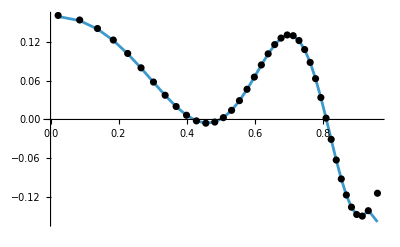

```mathematica
Show[ListLinePlot[Re[L13[[All,{1,2}]]]],ListPlot[Re[{#[[1]],#[[3]]}&/@L13],PlotStyle->{Black}]]
```

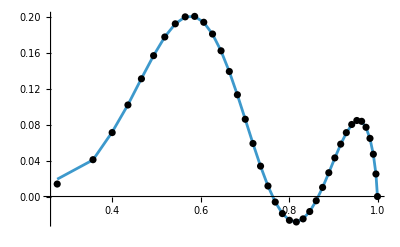

```mathematica
Show[ListLinePlot[Im[L13[[All,{1,2}]]]],ListPlot[Im[{#[[1]],#[[3]]}&/@L13],PlotStyle->{Black}]]
```

```mathematica
CMat41=DirectCMatN[setL,4,1,prec];
L4=Table[
Print[k];
findTrCA[setL,k,k,4,AMat,CMat41]
,{k,1,41,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

33

35

37

39

41

{{0.96148+0.274875 ⅈ,0.,0.+0. ⅈ},{0.934524+0.355899 ⅈ,0.,0.+0. ⅈ},{0.916834+0.399269 ⅈ,0.,0.+0. ⅈ},{0.900453+0.434952 ⅈ,0.,0.+0. ⅈ},{0.885045+0.465505 ⅈ,0.,0.+0. ⅈ},{0.869982+0.493084 ⅈ,0.,0.+0. ⅈ},{0.855128+0.518417 ⅈ,0.,0.+0. ⅈ},{0.840281+0.542151 ⅈ,0.,0.+0. ⅈ},{0.825372+0.56459 ⅈ,0.,0.+0. ⅈ},{0.810299+0.586017 ⅈ,0.,0.+0. ⅈ},{0.795015+0.60659 ⅈ,0.,0.+0. ⅈ},{0.779455+0.626458 ⅈ,0.,0.+0. ⅈ},{0.76358+0.645713 ⅈ,0.,0.+0. ⅈ},{0.747341+0.664441 ⅈ,0.,0.+0. ⅈ},{0.730699+0.6827 ⅈ,0.,0.+0. ⅈ},{0.713611+0.700542 ⅈ,0.,0.+0. ⅈ},{0.696039+0.718004 ⅈ,0.,0.+0. ⅈ},{0.677937+0.73512 ⅈ,0.,0.+0. ⅈ},{0.659265+0.75191 ⅈ,0.,0.+0. ⅈ},{0.639976+0.768395 ⅈ,0.,0.+0. ⅈ},{0.620023+0.784584 ⅈ,0.,0.+0. ⅈ}}

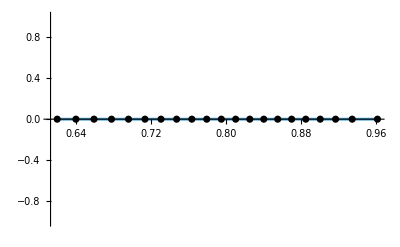

```mathematica
Show[ListLinePlot[Re[L4[[All,{1,2}]]]],ListPlot[Re[{#[[1]],#[[3]]}&/@L4],PlotStyle->{Black}]]
```

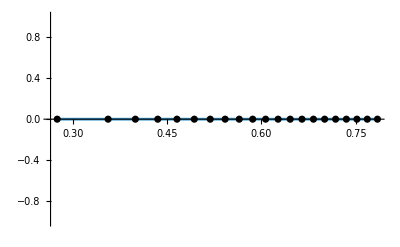

```mathematica
Show[ListLinePlot[Im[L4[[All,{1,2}]]]],ListPlot[Im[{#[[1]],#[[3]]}&/@L4],PlotStyle->{Black}]]
```

```mathematica
CMat51=DirectCMatN[setL,5,1,prec];
```

```mathematica
L5=Table[
Print[k];
findTrCA[setL,k,k,5,AMat,CMat51]
,{k,1,77,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

33

35

37

39

41

43

45

47

49

51

53

55

57

59

61

63

65

67

69

71

73

75

77

{{0.96148+0.274875 ⅈ,-1.55334+0.286538 ⅈ,-1.35113276984+0.249237595079 ⅈ},{0.934524+0.355899 ⅈ,-1.58936+0.720536 ⅈ,-1.58563386809+0.718844896857 ⅈ},{0.916834+0.399269 ⅈ,-1.51908+1.20067 ⅈ,-1.511040335434+1.194314987646 ⅈ},{0.900453+0.434952 ⅈ,-1.24007+1.60203 ⅈ,-1.238534124178+1.600054178024 ⅈ},{0.885045+0.465505 ⅈ,-0.82934+1.87979 ⅈ,-0.828860233659+1.878704749562 ⅈ},{0.869982+0.493084 ⅈ,-0.346922+1.99378 ⅈ,-0.347198971914+1.995329395554 ⅈ},{0.855128+0.518417 ⅈ,0.137722+1.93797 ⅈ,0.137903969759+1.940712408488 ⅈ},{0.840281+0.542151 ⅈ,0.561298+1.7274 ⅈ,0.562541878717+1.7313258791 ⅈ},{0.825372+0.56459 ⅈ,0.873597+1.40148 ⅈ,0.8760444802478+1.405483365518 ⅈ},{0.810299+0.586017 ⅈ,1.044+1.01269 ⅈ,1.047654473744+1.016277698095 ⅈ},{0.795015+0.60659 ⅈ,1.06561+0.620004 ⅈ,1.069930982416+0.622553426092 ⅈ},{0.779455+0.626458 ⅈ,0.953901+0.278176 ⅈ,0.958363582426+0.279483868498 ⅈ},{0.76358+0.645713 ⅈ,0.743596+0.0300597 ⅈ,0.747432340585+0.030315031763 ⅈ},{0.747341+0.664441 ⅈ,0.481153-0.0988768 ⅈ,0.483968079127-0.0994579685577 ⅈ},{0.730699+0.6827 ⅈ,0.217717-0.104147 ⅈ,0.219072381609-0.104719357974 ⅈ},{0.713611+0.700542 ⅈ,-3.22412×10^-6+0.0000802298 ⅈ,0.+0. ⅈ},{0.696039+0.718004 ⅈ,-0.135735+0.182759 ⅈ,-0.136711231226+0.184211800629 ⅈ},{0.677937+0.73512 ⅈ,-0.168638+0.404 ⅈ,-0.169906303405+0.407268567613 ⅈ},{0.659265+0.75191 ⅈ,-0.0949019+0.620122 ⅈ,-0.0957732275922+0.625174610324 ⅈ},{0.639976+0.768395 ⅈ,0.0723176+0.790309 ⅈ,0.0729201304308+0.7972786489636 ⅈ},{0.620023+0.784584 ⅈ,0.306912+0.883653 ⅈ,0.309907723819+0.8918734530908 ⅈ},{0.599352+0.800486 ⅈ,0.574689+0.881642 ⅈ,0.580124548433+0.8900187887879 ⅈ},{0.577907+0.816102 ⅈ,0.836644+0.779599 ⅈ,0.8451829007944+0.7872566381133 ⅈ},{0.555628+0.831431 ⅈ,1.0581+0.587346 ⅈ,1.068796927044+0.593230689825 ⅈ},{0.532446+0.846464 ⅈ,1.20897+0.32618 ⅈ,1.221456783087+0.329500559116 ⅈ},{0.508285+0.861189 ⅈ,1.27069+0.0258515 ⅈ,1.283854041527+0.026025153697 ⅈ},{0.483062+0.875586 ⅈ,1.23647-0.280306 ⅈ,1.248781682468-0.283124804374 ⅈ},{0.456679+0.889632 ⅈ,1.1097-0.558398 ⅈ,1.121437074518-0.564261436378 ⅈ},{0.429026+0.903292 ⅈ,0.908784-0.780263 ⅈ,0.9182240117181-0.7882694581052 ⅈ},{0.399976+0.916526 ⅈ,0.657863-0.924989 ⅈ,0.664276634354-0.9340596382707 ⅈ},{0.369374+0.929281 ⅈ,0.386435-0.981908 ⅈ,0.390022283548-0.990947214391 ⅈ},{0.337039+0.941491 ⅈ,0.125925-0.951404 ⅈ,0.127173683612-0.9597163156333 ⅈ},{0.302741+0.953073 ⅈ,-0.0947291-0.84539 ⅈ,-0.0954001405214-0.8522439800432 ⅈ},{0.266188+0.963921 ⅈ,-0.25382-0.684455 ⅈ,-0.255433898125-0.6896920810365 ⅈ},{0.226986+0.973898 ⅈ,-0.33823-0.496423 ⅈ,-0.340157776408-0.499437486186 ⅈ},{0.184568+0.98282 ⅈ,-0.34643-0.309342 ⅈ,-0.34786144661-0.311094519634 ⅈ},{0.138028+0.990428 ⅈ,-0.287223-0.151911 ⅈ,-0.287759751519-0.152174308672 ⅈ},{0.0856363+0.996326 ⅈ,-0.178279-0.0439281 ⅈ,-0.177831896598-0.044125841216 ⅈ},{0.0222687+0.999752 ⅈ,-0.0401516+0.000549346 ⅈ,-0.039096853313+0. ⅈ}}

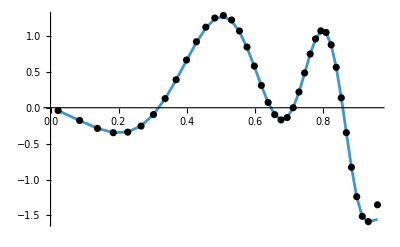

```mathematica
Show[ListLinePlot[Re[L5[[All,{1,2}]]]],ListPlot[Re[{#[[1]],#[[3]]}&/@L5],PlotStyle->{Black}]]
```

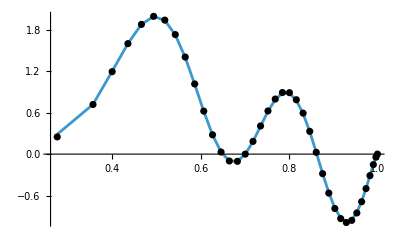

```mathematica
Show[ListLinePlot[Im[L5[[All,{1,2}]]]],ListPlot[Im[{#[[1]],#[[3]]}&/@L5],PlotStyle->{Black}]]
```

```mathematica
(*SAME exact {l1,l2,l3} as above but in a different order, so τ will be different (related by modular transformation). 
Note that tr(CA^{-1}) is still the same but tr(CA^{-1})/|\hat{f}(0)|^2 is not*)
L2=Table[
Print[k];
findTrCA[setL,setL/2-2k,k,AMat,CMat]
,{k,1,77,2}]
```

1

0.10184264651987+0.00206446406121 ⅈ

{1.+0. ⅈ,0.474144+3.38345 ⅈ,-0.474144+3.38345 ⅈ}

3

0.08513571053264+0.008657455580628 ⅈ

{1.+0. ⅈ,0.501515+2.72603 ⅈ,-0.501515+2.72603 ⅈ}

5

0.07420525664148+0.01368832147399 ⅈ

{1.+0. ⅈ,0.499669+2.39884 ⅈ,-0.499669+2.39884 ⅈ}

7

0.0650838154281+0.01755703015441 ⅈ

{1.+0. ⅈ,0.500116+2.18517 ⅈ,-0.500116+2.18517 ⅈ}

9

0.05695474068454+0.02043979193584 ⅈ

{1.+0. ⅈ,0.499948+2.02452 ⅈ,-0.499948+2.02452 ⅈ}

11

0.04953348875168+0.02245593786133 ⅈ

{1.+2.77556×10^-17 ⅈ,0.500027+1.89631 ⅈ,-0.500027+1.89631 ⅈ}

13

0.04270577552107+0.02370363913933 ⅈ

{1.-2.77556×10^-17 ⅈ,0.499984+1.78917 ⅈ,-0.499984+1.78917 ⅈ}

15

0.03642567566391+0.02427217063605 ⅈ

{1.+0. ⅈ,0.50001+1.69724 ⅈ,-0.50001+1.69724 ⅈ}

17

0.03067688236962+0.02424677854662 ⅈ

{1.+0. ⅈ,0.499994+1.61653 ⅈ,-0.499994+1.61653 ⅈ}

19

0.02545517064104+0.02371055074899 ⅈ

{1.-5.55112×10^-17 ⅈ,0.500005+1.54459 ⅈ,-0.500005+1.54459 ⅈ}

21

0.02075954320862+0.02274488541728 ⅈ

{1.+0. ⅈ,0.499997+1.47958 ⅈ,-0.499997+1.47958 ⅈ}

23

0.0165874749779+0.02142925101792 ⅈ

{1.+0. ⅈ,0.500002+1.42026 ⅈ,-0.500002+1.42026 ⅈ}

25

0.01293232077974+0.01984058166076 ⅈ

{1.+0. ⅈ,0.499998+1.3656 ⅈ,-0.499998+1.3656 ⅈ}

27

0.00978197548696+0.01805249756845 ⅈ

{1.+0. ⅈ,0.500001+1.3149 ⅈ,-0.500001+1.3149 ⅈ}

29

0.007118317126345+0.01613446471562 ⅈ

{1.+5.55112×10^-17 ⅈ,0.499999+1.26754 ⅈ,-0.499999+1.26754 ⅈ}

31

0.00491717062411+0.01415096690692 ⅈ

{1.-5.55112×10^-17 ⅈ,0.500001+1.22306 ⅈ,-0.500001+1.22306 ⅈ}

33

0.00314863363078+0.01216073959511 ⅈ

{1.-5.55112×10^-17 ⅈ,0.499999+1.18108 ⅈ,-0.499999+1.18108 ⅈ}

35

0.0017776609837+0.01021609942145 ⅈ

{1.+5.55112×10^-17 ⅈ,0.500001+1.14127 ⅈ,-0.500001+1.14127 ⅈ}

37

0.000764835205049+0.008362392872289 ⅈ

{1.-5.55112×10^-17 ⅈ,0.5+1.10337 ⅈ,-0.5+1.10337 ⅈ}

39

0.000067268662097+0.0066375796156 ⅈ

{1.-5.55112×10^-17 ⅈ,0.5+1.06715 ⅈ,-0.5+1.06715 ⅈ}

41

-0.00036040549528+0.005071959987812 ⅈ

{1.+0. ⅈ,0.5+1.03241 ⅈ,-0.5+1.03241 ⅈ}

43

-0.000564988663083+0.00368805120346 ⅈ

{1.+5.55112×10^-17 ⅈ,0.5+0.998989 ⅈ,-0.5+0.998989 ⅈ}

45

-0.000593647527214+0.00250061287678 ⅈ

{1.+0. ⅈ,0.5+0.966733 ⅈ,-0.5+0.966733 ⅈ}

47

-0.00049284444577+0.00151681923715 ⅈ

{1.-5.55112×10^-17 ⅈ,0.5+0.935513 ⅈ,-0.5+0.935513 ⅈ}

49

-0.00030728711912+0.000736572936623 ⅈ

{1.-5.55112×10^-17 ⅈ,0.5+0.905204 ⅈ,-0.5+0.905204 ⅈ}

51

-0.000078912524192+0.00015295359631 ⅈ

{1.+0. ⅈ,0.5+0.8757 ⅈ,-0.5+0.8757 ⅈ}

53

0.00015408512558-0.0002472067181 ⅈ

{1.+5.55112×10^-17 ⅈ,0.5+0.846896 ⅈ,-0.5+0.846896 ⅈ}

55

0.00035817897995-0.00048262892706 ⅈ

{1.+0. ⅈ,0.5+0.818698 ⅈ,-0.5+0.818698 ⅈ}

57

0.00050539174333-0.000576779954186 ⅈ

{1.-5.55112×10^-17 ⅈ,0.5+0.79101 ⅈ,-0.5+0.79101 ⅈ}

59

0.000574152828589-0.00055695721215 ⅈ

{1.+0. ⅈ,0.5+0.763741 ⅈ,-0.5+0.763741 ⅈ}

61

0.000550167626296-0.00045326313608 ⅈ

{1.+0. ⅈ,0.5+0.736793 ⅈ,-0.5+0.736793 ⅈ}

63

0.00042737077867-0.00029745884095 ⅈ

{1.+5.55112×10^-17 ⅈ,0.500001+0.710066 ⅈ,-0.500001+0.710066 ⅈ}

65

0.00020910207558-0.00012166879518 ⅈ

{1.+0. ⅈ,0.500001+0.683444 ⅈ,-0.500001+0.683444 ⅈ}

67

-0.000090215499072+0.00004312414496 ⅈ

{1.+0. ⅈ,0.500002+0.656793 ⅈ,-0.500002+0.656793 ⅈ}

69

-0.00044228411644+0.00016892041359 ⅈ

{1.+0. ⅈ,0.500003+0.629939 ⅈ,-0.500003+0.629939 ⅈ}

71

-0.000799515792967+0.00023315970143 ⅈ

{1.-2.77556×10^-17 ⅈ,0.500006+0.602645 ⅈ,-0.500006+0.602645 ⅈ}

73

-0.00108252333181+0.00022246419989 ⅈ

{1.+0. ⅈ,0.500016+0.574532 ⅈ,-0.500016+0.574532 ⅈ}

75

-0.00114263987349+0.0001396455645 ⅈ

{1.+6.93889×10^-18 ⅈ,0.500072+0.544898 ⅈ,-0.500072+0.544898 ⅈ}

77

-0.0005537291965+0.00002245864578 ⅈ

{1.+3.46945×10^-18 ⅈ,0.501896+0.5132 ⅈ,-0.501896+0.5132 ⅈ}

{{3.38345,0.251312},{2.72603,0.21033},{2.39884,0.183756},{2.18517,0.161735},{2.02452,0.1422},{1.89631,0.124399},{1.78917,0.108011},{1.69724,0.0928898},{1.61653,0.0789716},{1.54459,0.0662305},{1.47958,0.0546573},{1.42026,0.0442477},{1.3656,0.0349947},{1.3149,0.0268849},{1.26754,0.0198958},{1.22306,0.0139945},{1.18108,0.0091365},{1.14127,0.00526613},{1.10337,0.00231618},{1.06715,0.000208529},{1.03241,-0.00114522},{0.998989,-0.00184286},{0.966733,-0.00199047},{0.935513,-0.00170117},{0.905204,-0.00109356},{0.8757,-0.000289981},{0.846896,0.000585598},{0.818698,0.00141014},{0.79101,0.00206465},{0.763741,0.00243819},{0.736793,0.00243306},{0.710066,0.00197207},{0.683444,0.00100886},{0.656793,-0.000456108},{0.629939,-0.00234888},{0.602645,-0.00447261},{0.574532,-0.00640002},{0.544898,-0.00717038},{0.5132,-0.00369331}}

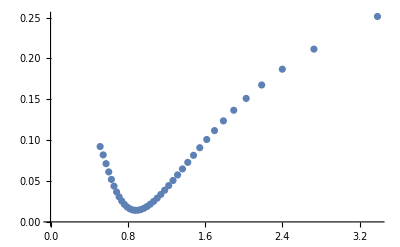

```mathematica
ListPlot[L2]
```

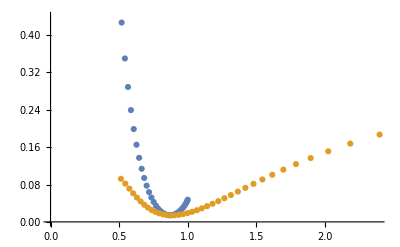

```mathematica
ListPlot[{L1,L2}] (*Don't match at equal τ2 values*)
```

Running test to see how well the values of tr(\wt{C} \wt{A}^{-1})/|\hat{f}(0)|^2 converge as L is increased

```mathematica
L31=Table[
Print[k];
findTrCA11[setL,2*k,k,AMat,CMat11]
,{k,1,31,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

{{0.951072+0.30958 ⅈ,0.0927827-0.0190954 ⅈ,0.0960742991532-0.007804243051211 ⅈ},{0.942985+0.399032 ⅈ,0.0746484-0.015403 ⅈ,0.0759851868376-0.01558916130085 ⅈ},{0.924931+0.456045 ⅈ,0.0615566-0.0208469 ⅈ,0.06200336020169-0.02075788121929 ⅈ},{0.908263+0.504204 ⅈ,0.0499376-0.0237168 ⅈ,0.05025148217636-0.02383473200774 ⅈ},{0.89134+0.546942 ⅈ,0.0398149-0.0250881 ⅈ,0.04001989656478-0.02517542644765 ⅈ},{0.874269+0.586672 ⅈ,0.0309684-0.0249778 ⅈ,0.03111701666957-0.02509285358092 ⅈ},{0.856622+0.624277 ⅈ,0.0233793-0.0237824 ⅈ,0.02348400027538-0.02388445051672 ⅈ},{0.838327+0.660533 ⅈ,0.0170144-0.0217324 ⅈ,0.01708588410052-0.02183472407361 ⅈ},{0.819154+0.695812 ⅈ,0.0118276-0.0191196 ⅈ,0.01187317347884-0.01920971218256 ⅈ},{0.798992+0.73048 ⅈ,0.00774479-0.0161677 ⅈ,0.007768967100684-0.01624907410823 ⅈ},{0.777647+0.764737 ⅈ,0.00465982-0.0130907 ⅈ,0.00466776012955-0.01315835600557 ⅈ},{0.754969+0.798796 ⅈ,0.00244523-0.0100479 ⅈ,0.0024404300597-0.01010279568669 ⅈ},{0.730749+0.832781 ⅈ,0.000956229-0.00716316 ⅈ,0.000942658737019-0.00720345155773 ⅈ},{0.704784+0.86683 ⅈ,0.0000442472-0.00450967 ⅈ,0.0000250881743-0.00453607905208 ⅈ},{0.676813+0.901024 ⅈ,-0.00043447-0.00212072 ⅈ,-0.00045603364765-0.00213290806139 ⅈ},{0.646549+0.93545 ⅈ,-0.000607544+0.0000119008 ⅈ,-0.000628713303172+0.00001274472005 ⅈ}}

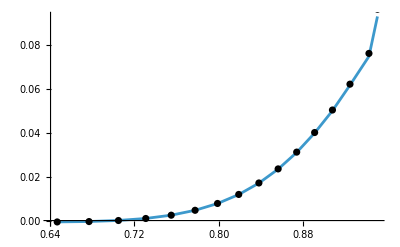

```mathematica
Show[ListLinePlot[Re[L31[[All,{1,2}]]]],ListPlot[Re[L31[[All,{1,3}]]],PlotStyle->{Black}]]
```

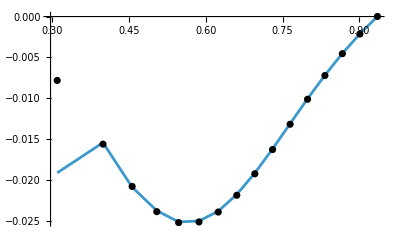

```mathematica
Show[ListLinePlot[Im[L31[[All,{1,2}]]]],ListPlot[Im[L31[[All,{1,3}]]],PlotStyle->{Black}]]
```

```mathematica
L32=Table[
Print[k];
findTrCA21[setL,2*k,k,AMat,CMat21]
,{k,1,31,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

{{0.951072+0.30958 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.942985+0.399032 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.924931+0.456045 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.908263+0.504204 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.89134+0.546942 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.874269+0.586672 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.856622+0.624277 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.838327+0.660533 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.819154+0.695812 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.798992+0.73048 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.777647+0.764737 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.754969+0.798796 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.730749+0.832781 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.704784+0.86683 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.676813+0.901024 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.646549+0.93545 ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

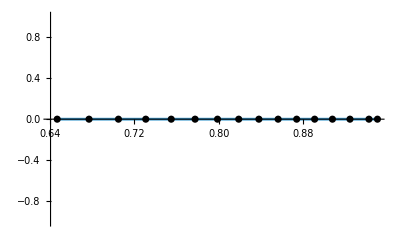

```mathematica
Show[ListLinePlot[Re[L32[[All,{1,2}]]]],ListPlot[Re[L32[[All,{1,3}]]],PlotStyle->{Black}]]
```

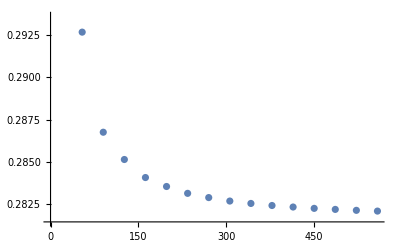

```mathematica
ListPlot[Table[{18*k,L3[[(k-1)/2+1,2]]},{k,1,31,2}]]
```

```mathematica
L33=Table[
Print[k];
findTrCA31[setL,2*k,k,AMat,CMat31]
,{k,1,31,2}]
```

1

3

5

7

9

11

13

15

17

19

21

23

25

27

29

31

{{0.951072+0.30958 ⅈ,-0.117759+0.0492519 ⅈ,-0.1237620004275+0.02026478483613 ⅈ},{0.942985+0.399032 ⅈ,-0.147138+0.0637491 ⅈ,-0.1481142756117+0.06383219625693 ⅈ},{0.924931+0.456045 ⅈ,-0.143803+0.111081 ⅈ,-0.1440945761578+0.110163649888 ⅈ},{0.908263+0.504204 ⅈ,-0.120455+0.151892 ⅈ,-0.1205864121481+0.1517567081473 ⅈ},{0.89134+0.546942 ⅈ,-0.0823542+0.182819 ⅈ,-0.082580158993139+0.18267818205471 ⅈ},{0.874269+0.586672 ⅈ,-0.0356704+0.198864 ⅈ,-0.035821950035242+0.19894554489414 ⅈ},{0.856622+0.624277 ⅈ,0.0134655+0.198797 ⅈ,0.01331096834304+0.19897142757102 ⅈ},{0.838327+0.660533 ⅈ,0.0586719+0.183406 ⅈ,0.058624349143843+0.18368635380143 ⅈ},{0.819154+0.695812 ⅈ,0.0949916+0.155918 ⅈ,0.095020683502614+0.15625220652663 ⅈ},{0.798992+0.73048 ⅈ,0.119095+0.12106 ⅈ,0.11924463652199+0.12140548804469 ⅈ},{0.777647+0.764737 ⅈ,0.130057+0.0842275 ⅈ,0.13029620713438+0.084552813397956 ⅈ},{0.754969+0.798796 ⅈ,0.129112+0.050526 ⅈ,0.12943395702518+0.050789781995817 ⅈ},{0.730749+0.832781 ⅈ,0.119409+0.0238326 ⅈ,0.11977741063394+0.02402542363649 ⅈ},{0.704784+0.86683 ⅈ,0.105211+0.00625925 ⅈ,0.1055957633426+0.006368739859412 ⅈ},{0.676813+0.901024 ⅈ,0.0910534-0.00216321 ⅈ,0.09142671893966-0.00212130279895 ⅈ},{0.646549+0.93545 ⅈ,0.0808541-0.0032824 ⅈ,0.08119537424503-0.00329319486943 ⅈ}}

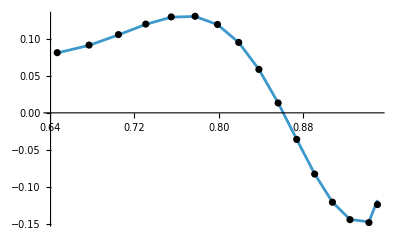

```mathematica
Show[ListLinePlot[Re[L33[[All,{1,2}]]]],ListPlot[Re[{#[[1]],#[[3]]}&/@L33],PlotStyle->{Black}]]
```

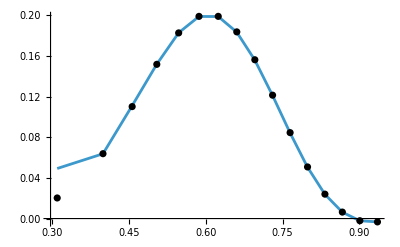

```mathematica
Show[ListLinePlot[Im[L33[[All,{1,2}]]]],ListPlot[Im[{#[[1]],#[[3]]}&/@L33],PlotStyle->{Black}]]
```

```mathematica
L15={{0.961480094317146+0.2748745681799191 ⅈ,-1.5533374354291087+0.2865379226239157 ⅈ,-1.35113276983703665284391213118530523829`12.962897819499029+0.24923759507946385378620298581036949925`12.45130160098784 ⅈ},{0.934524466513451+0.35589889222602267 ⅈ,-1.5893593347364676+0.7205364093144992 ⅈ,-1.58563386809000378321535959270220860942`13.093889475329897+0.71884489685652546465361837224357375305`12.88318295278303 ⅈ},{0.9168338770293087+0.39926888425152374 ⅈ,-1.5190771940384573+1.2006683421331026 ⅈ,-1.51104033543375314008252631103666253181`13.124228698152995+1.1943149876456638085760627780739327164`13.083175584425568 ⅈ},{0.9004534257711199+0.43495244339712136 ⅈ,-1.2400669543868976+1.602033517655157 ⅈ,-1.23853412417754209322622299715753149694`13.092397539968664+1.60005417802417868647502266314262968457`13.205363583682443 ⅈ},{0.8850450747028868+0.4655053337440107 ⅈ,-0.8293402680323934+1.8797932803966955 ⅈ,-0.82886023365934930105529180419732564795`12.974215989208249+1.87870474956217691960998730801781040927`13.280320534428657 ⅈ},{0.8699816351767246+0.4930841251300794 ⅈ,-0.3469223404101096+1.9937785514897517 ⅈ,-0.3471989719143759659331724683128459629`12.645344928990601+1.99532939555403143041044896741373307938`13.3221737379677 ⅈ},{0.8551278677317259+0.5184171388260644 ⅈ,0.13772152717899083+1.9379687206446539 ⅈ,0.13790396975876398884087980861797503629`12.266278753014513+1.94071240848775688633771100059000110712`13.329660144656275 ⅈ},{0.8402813400573641+0.54215059674535 ⅈ,0.5612976202408015+1.7273979643079207 ⅈ,0.56254187871723119839743635355214976259`12.842145810617783+1.73132587909966051611475134166009319548`13.316575059668475 ⅈ},{0.82537168462013+0.5645897468314707 ⅈ,0.8735968048924223+1.4014809170687033 ⅈ,0.87604448024782350926132134714268690286`13.020774950631502+1.4054833655180981075657627239066059121`13.220134408598101 ⅈ},{0.8102987271464833+0.5860170413774608 ⅈ,1.0439963997865382+1.0126868757597762 ⅈ,1.04765447374436895295348418241887591623`13.074015012681224+1.01627769809473826991129767754458596197`13.096496299621807 ⅈ},{0.7950145492133673+0.606590361396392 ⅈ,1.0656141439688818+0.6200038534045885 ⅈ,1.06993098241559525370854451156466000988`13.06108661312972+0.62255342609196117991938926058811161097`12.913002979294752 ⅈ},{0.7794548841242537+0.626458365428057 ⅈ,0.9539007899182099+0.2781760425635075 ⅈ,0.95836358242580681033183953967647277382`12.99708202236769+0.27948386849782902340153272484762736256`12.608444732535558 ⅈ},{0.7635802147910723+0.6457129823533438 ⅈ,0.7435961704692506+0.030059722604810143 ⅈ,0.74743234058527506844761699514907357268`12.882242418852217+0.03031503176318692035205597274426416662`11.694136009382824 ⅈ},{0.747340721799569+0.6644410023020264 ⅈ,0.4811530395631873-0.09887683239258374 ⅈ,0.48396807912693905386434992081602223476`12.698405629994838-0.09945796855768779997764449962299291934`12.191091638749565 ⅈ},{0.73069923223181+0.6826995181013517 ⅈ,0.2177165157198733-0.10414658087738161 ⅈ,0.21907238160916042207962942841096480862`12.373526137909918-0.10471935797421518406439993687647491519`12.170762576636058 ⅈ},{0.7136112517647543+0.7005419197698166 ⅈ,-3.2241171039615324*^-6+0.0000802298343309249 ⅈ,0``13.064881009401448+0``13.11975839452701 ⅈ},{0.6960385960400922+0.7180043682475425 ⅈ,-0.1357352009505405+0.18275851704912424 ⅈ,-0.13671123122620496353354195044503546481`12.242921281541726+0.18421180062935747680456743382741990581`12.369353547361872 ⅈ},{0.6779372102876858+0.7351198126206058 ⅈ,-0.16863807291924146+0.4040001647943007 ⅈ,-0.16990630340493114675953615714083650668`12.382794722754058+0.40726856761277889701101844644952951279`12.714026314506459 ⅈ},{0.6592654743166477+0.7519102568618464 ⅈ,-0.09490186044438798+0.6201222620225035 ⅈ,-0.09577322759224575684244031749962806059`12.166851896127929+0.625174610323662657117475337309417305`12.914184861226808 ⅈ},{0.6399764300090507+0.7683945399551535 ⅈ,0.07231761355014901+0.7903093099547689 ⅈ,0.07292013043084320625380223694279344966`12.052663820150569+0.79727864896361577448465319334183852831`13.03935362076085 ⅈ},{0.6200227489450637+0.7845838328633862 ⅈ,0.30691203515684384+0.8836532590007742 ⅈ,0.3099077238189029059044195682834176448`12.66974376733634+0.89187345309077440100004119154456750254`13.112690408577958 ⅈ},{0.5993516015047777+0.8004858885537336 ⅈ,0.5746892887622408+0.8816418054700661 ⅈ,0.58012454843336436016965075130637450015`12.934489522489892+0.89001878878794491494523746332636869465`13.13647547465896 ⅈ},{0.5779073226368239+0.816102399483505 ⅈ,0.8366439720073122+0.7795990411816247 ⅈ,0.84518290079442287666106571921825219371`13.093532478634172+0.78725663811327978325971653581004482357`13.101646353096662 ⅈ}};
```

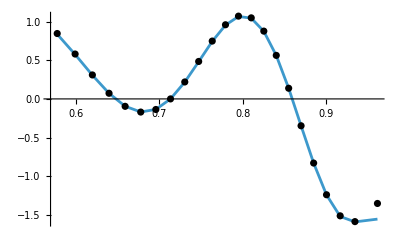

```mathematica
Show[ListLinePlot[Re[L15[[All,{1,2}]]]],ListPlot[Re[{#[[1]],#[[3]]}&/@L15],PlotStyle->{Black}]]
```

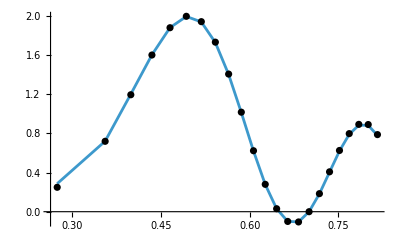

```mathematica
Show[ListLinePlot[Im[L15[[All,{1,2}]]]],ListPlot[Im[{#[[1]],#[[3]]}&/@L15],PlotStyle->{Black}]]
```